# ModeCode Mockup

## Basics building blocks

#### Choose the number of fields and Npivot

```mathematica
d=2;
Npivot=55;
Nsubhorizon=10;
```

#### Fields, mometa, modes

[JF] Might want to make ψαβ and παβ symmetric (if they are indeed symmetric!) for speed purpouses

```mathematica
ϕα = Table[Symbol["ϕ" <> ToString[i]][t], {i, d}];
pα = Table[Symbol["p" <> ToString[i]][t], {i, d}];

ψαβ = Table[Symbol["ψ" <> ToString[i]<>ToString[j]][t], {i, d}, {j, d}];
παβ = Table[Symbol["π" <> ToString[i]<>ToString[j]][t], {i, d}, {j, d}];
Print["ψαβ = ",ψαβ//MatrixForm," ", "παβ = ",παβ//MatrixForm ]
```

ψαβ = (ψ11[t] | ψ12[t]
ψ21[t] | ψ22[t]) παβ = (π11[t] | π12[t]
π21[t] | π22[t])

```mathematica
ϕparameters = Table[Symbol["ϕ" <> ToString[i]], {i, d}];
pparameters = Table[Symbol["p" <> ToString[i]], {i, d}];
ψparameters=Flatten[ Table[Symbol["ψ" <> ToString[i]<>ToString[j]], {i, d}, {j, d}]];
πparameters = Flatten[Table[Symbol["π" <> ToString[i]<>ToString[j]], {i, d}, {j, d}]];

backgroundparameters=Join[ϕparameters,pparameters];
allparameters=Join[backgroundparameters,ψparameters,πparameters]
```

{ϕ1,ϕ2,p1,p2,ψ11,ψ12,ψ21,ψ22,π11,π12,π21,π22}

### Potentials and background initial conditions

#### Double quadratic

```mathematica
ϕIC={10.31001803105938,12.93651907528955};
M=10^-5;
mϕ=1M;
mχ=9M;
W=1/2 mϕ^2 ϕ1[t]^2+1/2 mχ^2 ϕ2[t]^2;
```

### Background quantities

```mathematica
H=Sqrt[W/(3-ϵ)];

ϵ=1/2 pα.pα;

ϵSR=1/2(Wα.Wα)/W^2;
HSR=Sqrt[W/3];
Wα=Map[D[W,#]&,ϕα];
Wαβ=Outer[D[#1,#2]&,Wα,ϕα];
```

### Stuff for plotting

```mathematica
Labels=Directive[Darker[Blue],FontFamily->"Helvetica Neue",FontSize->12];
ThickBlue=Directive[Thick,Blue];
ThickRed=Directive[Thick,Red];
ThickOrange=Directive[Thick,Orange];
ThickGreen=Directive[Thick,Green];
ThickPurple=Directive[Thick,Purple];
ThickYellow=Directive[Thick,Darker[Yellow,0.2]];
ThickDarkRed=Directive[Thick,Blend[{Red,Blue},0.15]];
```

## Solve for the background to get ICs for the mode eqations

### Prepare background equations for solver

#### Initial conditions (N.B this uses SLOW-ROLL ICs)

[JF] N.B this uses slow-roll initial conditions
[JF] N.B pinitialsub is not needed until the perturbations section of the code

```mathematica
ϕinitialsub=Thread[Rule[ϕα,ϕIC]];
ϕinitial=Thread[(ϕα/.t->0)==ϕIC]
pIC=First[-Wα/W/.{ϕinitialsub}];
pinitialsub=Thread[Rule[pα,pIC]];
(*pIC={0,0};*)
pinitial=Thread[(pα/.t->0)==pIC]
```

{ϕ1[0]==10.31,ϕ2[0]==12.9365}

{p1[0]==-0.00150931,p2[0]==-0.153398}

#### Background (Klein--Gordon split up for a bit of excitement)

[JF] N.B this use of mapping is not your usual way. UPDATE: changed it now but it is actually very slightly slower using a list of equations rather than the vector structure you had
[JF] This splitting seems to be slower than using the second order equation....Maybe you should check this, and try to understand why.

```mathematica
KG=Join[Table[D[ϕα[[i]], t]==pα[[i]],{i,d}],Table[D[pα[[i]], t]==-(3-ϵ)pα[[i]]-(3-ϵ)Wα[[i]]/W,{i,d}]];
(*KG//MatrixForm*)
```

```mathematica
tmin=0;
tmax=10000;
allbackgroundequations=Join[KG,ϕinitial,pinitial];
```

### Solve!

```mathematica
Timing[backgroundsol=NDSolve[allbackgroundequations,backgroundparameters,{t,tmin,tmax},MaxSteps->∞]]
```

NDSolve::ndsz: At t == 74.8636, step size is effectively zero; singularity or stiff system suspected.

{12.91536,{{ϕ1→InterpolatingFunction[{{0.,74.8636}},<>],ϕ2→InterpolatingFunction[{{0.,74.8636}},<>],p1→InterpolatingFunction[{{0.,74.8636}},<>],p2→InterpolatingFunction[{{0.,74.8636}},<>]}}}

### Find Nend

[JF] Do not currently have an accurate automated method of finding when ϵ=1. For now use FindRoot with two different methods (controlled by number of starting values) and plotting to find a believable answer. Currently the first method seems to agree with ModeCode.
[JF] Layne has a really cool way of doing this! Don’t know how reliable it is but certainly much neater and will also be faster since N.D solve looses a lot of time dealing with a stiff system you don’t care about.

```mathematica
accend = FindRoot[1==Re[ϵ]/.backgroundsol,{t,70},AccuracyGoal->Infinity,PrecisionGoal->10];Nend = t/.accend
accend1= FindRoot[1==Re[ϵ]/.backgroundsol,{t,69,75},AccuracyGoal->Infinity,PrecisionGoal->10];Nend1 = t/.accend1
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

69.6815

InterpolatingFunction::dmval: Input value {75.} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

72.1573

## Output from background solution

### Background plots

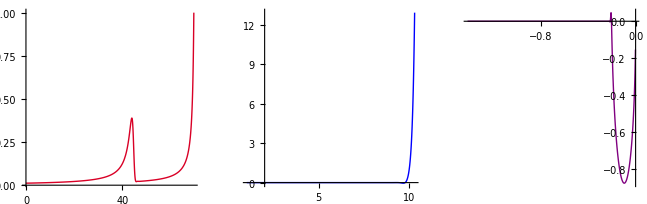

```mathematica
GraphicsRow[{
Plot[Re[ϵ]/.backgroundsol,{t,0,Nend},
PlotStyle->ThickDarkRed,PlotRange->All],

ParametricPlot[ϕα/.backgroundsol,{t,0,Nend},PlotStyle->ThickBlue,PlotRange->All],

ParametricPlot[pα/.backgroundsol,{t,0,Nend},PlotStyle->ThickPurple,PlotRange->All]
}]
```

### Useful quantities

```mathematica
Print["N_(exit temp)"]
Nexittemp=Nend-Npivot
Print["H_exit"]
Hexit=First[H/.backgroundsol/.t->Nexittemp]
Print["ϵ_exit"]
ϵexit=First[ϵ/.backgroundsol/.t->Nexittemp]
Print["ϕ_α^exit"]
ϕexit=First[ϕα/.backgroundsol/.t->Nexittemp]

Print["N_(BD temp)"]
NBDtemp=Nexittemp-Nsubhorizon
Print["H_BD"]
HBD=First[H/.backgroundsol/.t->NBDtemp]
Print["ϵ_BD"]
ϵBD=First[ϵ/.backgroundsol/.t->NBDtemp]
Print["ϕ_α^BD"]
ϕBD=First[ϕα/.backgroundsol/.t->NBDtemp]
Print["p_α^BD"]
pBD=First[pα/.backgroundsol/.t->NBDtemp]

If[NBDtemp≤0,
Print["YOU CAN NOT COUNT e-folds CORRECTLY"],
Print["YOUR MODEL LOOKS GOOD!"]
]
```

N_(exit temp)

14.6815

H_exit

0.000387826

ϵ_exit

0.0176413

ϕ_α^exit

{10.2832,10.462}

N_(BD temp)

4.68145

H_BD

0.00045123

ϵ_BD

0.0130906

ϕ_α^BD

{10.3026,12.2005}

p_α^BD

{-0.00167949,-0.161797}

YOUR MODEL LOOKS GOOD!

## Solve for the perturbations

[JF] You can’t start with Bunch--Davies initital conditions at the beginning of inflation. See Pesky & Schroeder. Instead, they should start say 5 or 10 e-folds beofore horizon exit. For this reason, you might as well reset N such that N=0 corresponds to horizon crossing. 
[JF] ModeCode uses a_exit H_exit=k/100. i.e you are far far more subhorizon....is this a problem?

### Quantities obtained from background solution

[JF] Define N_BD to be the time associated with Bunch--Davies initial conditions.

```mathematica
Nexit=0;
NBD=Nexit-Nsubhorizon;
k=ⅇ^Nexit Hexit;
aBD=ⅇ^NBD;
Print["k = ", k]
Print["k/a_BD = ", k/(aBD HBD)]
```

k = 0.000387826

k/a_BD = 18931.5

[JF] Be wary of this definition of of the scalefactor a

```mathematica
a=ⅇ^t;
```

#### Initial conditions

[JF] Confused about thiese initial conditions. Why is e^(ⅈk/aH)=1 ?! On subhorizon scales 1/k<<1/aHso.....wtf!

```mathematica
ψBDstart=Thread[(Flatten[ψαβ]/.t->NBD)==Flatten[IdentityMatrix[d]*1/(√(2k))]];
πBDstart=Thread[(Flatten[παβ]/.t->NBD)==Flatten[IdentityMatrix[d]*(- ⅈ)/(aBD HBD)√(k/2)]];
(*ψBDstart=Thread[(Flatten[ψαβ]/.t->NBD)==Flatten[IdentityMatrix[d]*1/(√(2k))ⅇ^((ⅈ k)/(aBD HBD))]];
πBDstart=Thread[(Flatten[παβ]/.t->NBD)==Flatten[IdentityMatrix[d]*(- ⅈ)/(aBD HBD)√(k/2)ⅇ^((ⅈ k)/(aBD HBD))]];*)
Print["Possibly require a factor of ",ⅇ^(ⅈ k/(aBD HBD))]
```

Possibly require a factor of 0.976239+0.216697 ⅈ

```mathematica
ϕBDstart=Thread[(ϕα/.t->NBD)==ϕBD];
pBDstart=Thread[(pα/.t->NBD)==pBD];
```

### Equation of motion for the modes

#### Mass Matrix

```mathematica
Cαβ=Table[Wαβ[[i,j]]/H^2+1/H^2(pα[[i]]Wα[[j]]+Wα[[i]]pα[[j]])+(3-ϵ)pα[[i]]pα[[j]],{i,d},{j,d}];
(*Cαβ//MatrixForm*)
```

#### Equation of motion (split again for no good reason)

```mathematica
ψEq=Flatten[Table[D[ψαβ[[i,j]], t]==παβ[[i,j]],{i,d},{j,d}]];
πEq=Flatten[Table[D[παβ[[i,j]], t]==-(1-ϵ)παβ[[i,j]]-(k^2/(a^2 H^2)-2+ϵ)ψαβ[[i,j]]-Sum[Cαβ[[i,l]]ψαβ[[j,l]],{l,d}],{i,d},{j,d}]];
(*ψEq//MatrixForm
πEq//MatrixForm*)
```

```mathematica
allequations=Join[KG,ψEq,πEq,ϕBDstart,pBDstart,ψBDstart,πBDstart];
```

### Solve for everything!!!

[JF] Full solution includes background equations and mode equations. Not sure if this is the best way to do it but stick with it for now.
[JF] Neither code works but right now but Lyne’s does the equivalent solve in 12.05 seconds compared with your 5.2....I would have epected his method to be quicker than this one. 
[JF] Also, it looks like you start deeper subhorizon which massively slows your code down. If you start Nsubhorizon = 4 the solve takes 0.093963 seconds.

```mathematica
Timing[fullsol=NDSolve[allequations,allparameters,{t,NBD,Npivot},MaxSteps->∞]]
```

{5.26344,{{ϕ1→InterpolatingFunction[{{-10.,55.}},<>],ϕ2→InterpolatingFunction[{{-10.,55.}},<>],p1→InterpolatingFunction[{{-10.,55.}},<>],p2→InterpolatingFunction[{{-10.,55.}},<>],ψ11→InterpolatingFunction[{{-10.,55.}},<>],ψ12→InterpolatingFunction[{{-10.,55.}},<>],ψ21→InterpolatingFunction[{{-10.,55.}},<>],ψ22→InterpolatingFunction[{{-10.,55.}},<>],π11→InterpolatingFunction[{{-10.,55.}},<>],π12→InterpolatingFunction[{{-10.,55.}},<>],π21→InterpolatingFunction[{{-10.,55.}},<>],π22→InterpolatingFunction[{{-10.,55.}},<>]}}}

## Output from full solution

[JF] Check background still looks sensible.

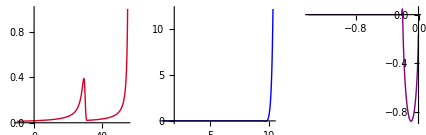

```mathematica
GraphicsRow[{
Plot[Re[ϵ]/.fullsol,{t,NBD,Npivot},
PlotStyle->ThickDarkRed,PlotRange->All],

ParametricPlot[ϕα/.fullsol,{t,NBD,Npivot},PlotStyle->ThickBlue,PlotRange->All],

ParametricPlot[pα/.fullsol,{t,NBD,Npivot},PlotStyle->ThickPurple,PlotRange->All]
}]
```

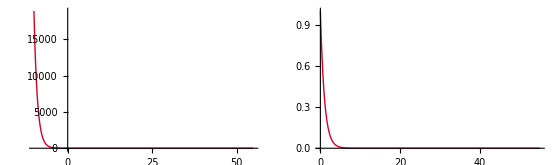

```mathematica
GraphicsRow[{Plot[k/(a H)/.fullsol,{t,NBD,Npivot},
PlotStyle->ThickDarkRed,PlotRange->All],Plot[k/(a H)/.fullsol,{t,Nexit,Npivot},
PlotStyle->ThickDarkRed,PlotRange->All]}]
```

[JF] The real part of the modes plotted twice. Once just for the subhorizon evolutoin, once just for the superhorizon evolution.

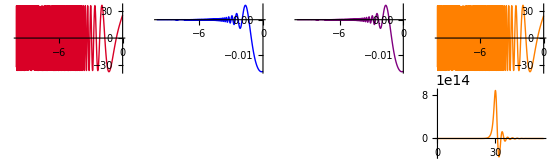

```mathematica
GraphicsGrid[{{
Plot[Re[ψ11[t]]/.fullsol,{t,NBD,Nexit},PlotStyle->ThickDarkRed,PlotRange->All],
Plot[Re[ψ12[t]]/.fullsol,{t,NBD,Nexit},PlotStyle->ThickBlue,PlotRange->All],
Plot[Re[ψ21[t]]/.fullsol,{t,NBD,Nexit},PlotStyle->ThickPurple,PlotRange->All],
Plot[Re[ψ22[t]]/.fullsol,{t,NBD,Nexit},PlotStyle->ThickOrange,PlotRange->All]
},{
Plot[Re[ψ11[t]]/.fullsol,{t,Nexit,Npivot},PlotStyle->ThickDarkRed,PlotRange->All],
Plot[Re[ψ12[t]]/.fullsol,{t,Nexit,Npivot},PlotStyle->ThickBlue,PlotRange->All],
Plot[Re[ψ21[t]]/.fullsol,{t,Nexit,Npivot},PlotStyle->ThickPurple,PlotRange->All],
Plot[Re[ψ22[t]]/.fullsol,{t,Nexit,Npivot},PlotStyle->ThickOrange,PlotRange->All]
}}]
```

## Observables

### Powerspectrum

```mathematica
Pαβ=k^3/(2 π^2)Table[Sum[ψαβ[[i,l]]/a((ψαβ[[j,l]])*)/a,{l,d}],{i,d},{j,d}];
```

```mathematica
ωζ=pα/(√(2 ϵ));
```

```mathematica
Pζ=1/(2ϵ)Sum[ωζ[[i]]ωζ[[j]]Pαβ[[i,j]],{i,d},{j,d}];
Evaluate[Pζ/.fullsol/.t->Npivot]
(2π)/k^3 Evaluate[Pζ/.fullsol/.t->Npivot]
```

{2.02427×10^-6+0. ⅈ}

{218040.+0. ⅈ}

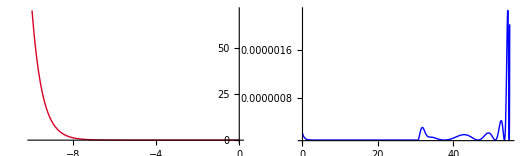

```mathematica
GraphicsRow[{Plot[Pζ/.fullsol,{t,NBD,Nexit},
PlotStyle->ThickDarkRed,PlotRange->All],
Plot[Pζ/.fullsol,{t,Nexit,Npivot},
PlotStyle->ThickBlue,PlotRange->All]}]
```

[JF] NB time range

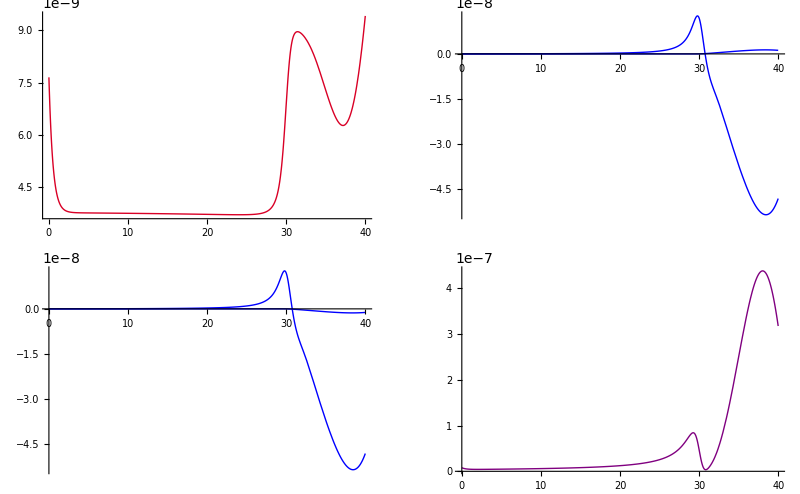

```mathematica
GraphicsGrid[{{
Plot[Pαβ[[1,1]]/.fullsol,{t,Nexit,40},
PlotStyle->ThickDarkRed,PlotRange->All],
Plot[{Re[Pαβ[[1,2]]],Im[Pαβ[[1,2]]]}/.fullsol,{t,Nexit,40},
PlotStyle->{ThickBlue},PlotRange->All]
},{
Plot[{Re[Pαβ[[2,1]]],Im[Pαβ[[2,1]]]}/.fullsol,{t,Nexit,40},
PlotStyle->{ThickBlue},PlotRange->All],Plot[Pαβ[[2,2]]/.fullsol,{t,Nexit,40},
PlotStyle->ThickPurple,PlotRange->All]
}}]
```